```mathematica
aaaa=ResourceFunction["SetPartitions"][{Atree[{k[1],in[12],in[8]}],
Atree[{k[2],in[5],-in[12]}],
Atree[{-in[5],in[6],in[9]}],
Atree[{-in[6],in[7],in[10]}],
Atree[{-in[10],in[14],in[11]}],
Atree[{-in[11],-in[8],-in[9]}],
 Atree[{-in[7],in[13],k[3]}],
 Atree[{-in[14],-in[13],k[4]}]}]
```

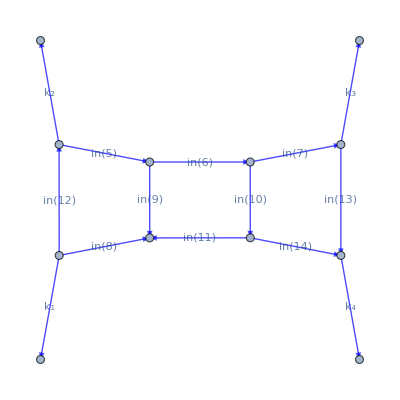

```mathematica
aaaa[[1]][[1]]//toGraph// doOrderedPlot[#,k/@Range[4]]&
```

```mathematica
sewGraphs[(aaaa[[2]][[1]]//treesToLoops)[[1]],(aaaa[[2]][[2]]//treesToLoops)[[1]]]//doOrderedPlot[#,k/@Range[4]]&
```

-Graphics-

Cut function changes a cut legs to l:

```mathematica
Cut[aaaa[[2]],in[5]]
```

{{A_3^tree(k_1,in[12],in[8])},{A_3^tree(k_2,l_1,-in[12]),A_3^tree(-l_1,in[6],in[9]),A_3^tree(-in[6],in[7],in[10]),A_3^tree(-in[10],in[14],in[11]),A_3^tree(-in[11],-in[8],-in[9]),A_3^tree(-in[7],in[13],k_3),A_3^tree(-in[14],-in[13],k_4)}}

Cut1 function changes all legs into l:

```mathematica
Cut1[aaaa[[2]]]
```

{{A_3^tree(k_1,l_1,l_1)},{A_3^tree(k_2,l_1,-l_1),A_3^tree(-l_1,l_1,l_1),A_3^tree(-l_1,l_1,l_1),A_3^tree(-l_1,l_1,l_1),A_3^tree(-l_1,-l_1,-l_1),A_3^tree(-l_1,l_1,k_3),A_3^tree(-l_1,-l_1,k_4)}}

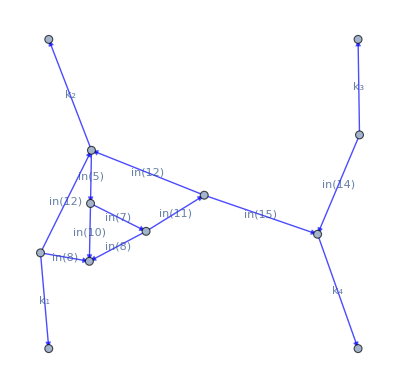
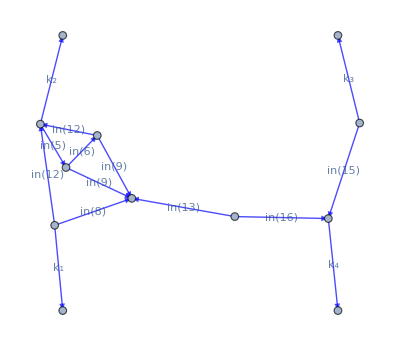
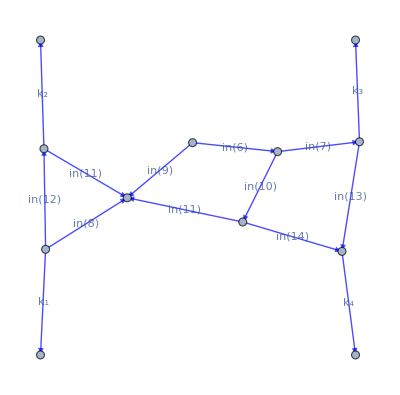
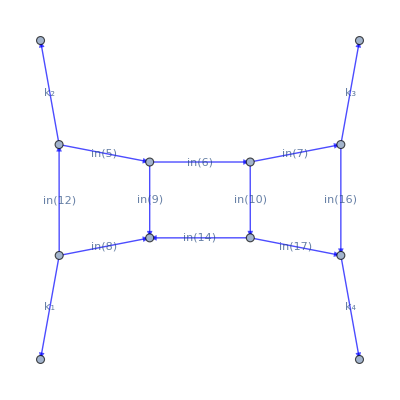
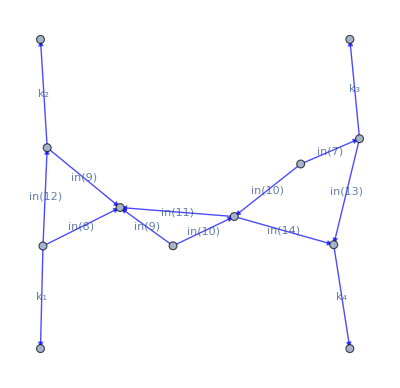
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
bbbbbb=Table[Sew3[aaaa[[i]]],{i,1,10}]
```

```mathematica
SewTest1[bbbbb][[1]]===SewTest1[bbbbb][[2]]
```

True

```mathematica
SewTest2[bbbbb]
```

{0,1,3,6,7}